{Binding Energy cs, bs, cc, bc, bb}

-0.0241966

-0.0304985

-0.0762821

-0.0988409

-0.125162

{Ωc 1/2+ 2.695}

{2.67983,4.93219,{3.07934,2.95553,2.48389,2.04279}}

{0.28009}

{{-0.405819},{-0.384388}}

{Ωc^* 3/2+ 2.766}

{2.76393,5.09833,{3.08135,2.96114,2.49351,2.04279}}

{0.288724}

{{-0.339228},{-0.321313}}

{Ds 0- 1.968}

{1.96085,3.7729,{3.06048,2.90455,2.40967,2.04279}}

{0.460343,0.460343}

{Ds^* 1- 2.112}

{2.112,4.17223,{3.06814,2.92487,2.43672,2.04279}}

{0.505275,0.505275}

{{0.409478,-0.409478},{0.387854,-0.387854}}

{Ωb 1/2+ 6.046}

{6.07965,4.76789,{3.07721,2.94963,2.47414,2.04279}}

{0.595299}

{{-0.324028},{-0.306917}}

{Ωb^* 3/2+}

{6.11174,4.84462,{3.07822,2.95243,2.47872,2.04279}}

{0.604302}

{{-0.540635},{-0.512084}}

{Bs 0- 5.367}

{5.34633,3.35236,{3.05051,2.87886,2.37929,2.04279}}

{0.157977,0.157977}

{Bs^* 1- 5.415}

{5.415,3.61961,{3.05711,2.89576,2.39883,2.04279}}

{0.16932,0.16932}

{{0.380241,-0.380241},{0.360161,-0.360161}}

{ηc 0- 2.984}

{3.00159,3.15293,{3.04487,2.86475,2.36417,2.04279}}

{0.}

{Jψ 1- 3.097}

{3.097,3.54182,{3.05529,2.89105,2.39323,2.04279}}

{0.}

{{0.},{0.}}

{Bc 0- 6.275}

{6.275,2.53308,{3.02194,2.81029,2.31393,2.04279}}

{0.294561,0.294561}

{Bc^* 1-}

{6.33337,2.81538,{3.03359,2.83735,2.33744,2.04279}}

{0.324545,0.324545}

{{0.198076,-0.198076},{0.187616,-0.187616}}

{ηb 0- 9.399}

{9.39655,1.59285,{2.95593,2.67777,2.22713,2.04279}}

{0.}

{Υ 1- 9.460}

{9.46,1.79922,{2.97583,2.71425,2.24739,2.04279}}

{0.}

{{0.},{0.}}

{Ξcc 1/2+ 3.621}

{3.60292,4.42097,{3.07222,2.93592,2.45276,2.04279}}

{0.778507,0.448939}

{{0.0471353,0.34525},{0.0446461,0.327017}}

{Ξcc^* 3/2+ 1.533}

{3.7132,4.63809,{3.07543,2.94471,2.46627,2.04279}}

{0.815103,0.468141}

{{0.997157,0.0588909},{0.944497,0.0557809}}

{Ξbb 1/2+}

{10.3075,3.70758,{3.05908,2.90088,2.40508,2.04279}}

{0.287476,0.449293}

{{-0.209594,0.0404155},{-0.198525,0.0382812}}

{Ξbb^* 3/2+}

{10.3565,3.86583,{3.0624,2.9096,2.41611,2.04279}}

{0.300246,0.468152}

{{0.456896,-0.325146},{0.432767,-0.307975}}

{Mass Spectrum}

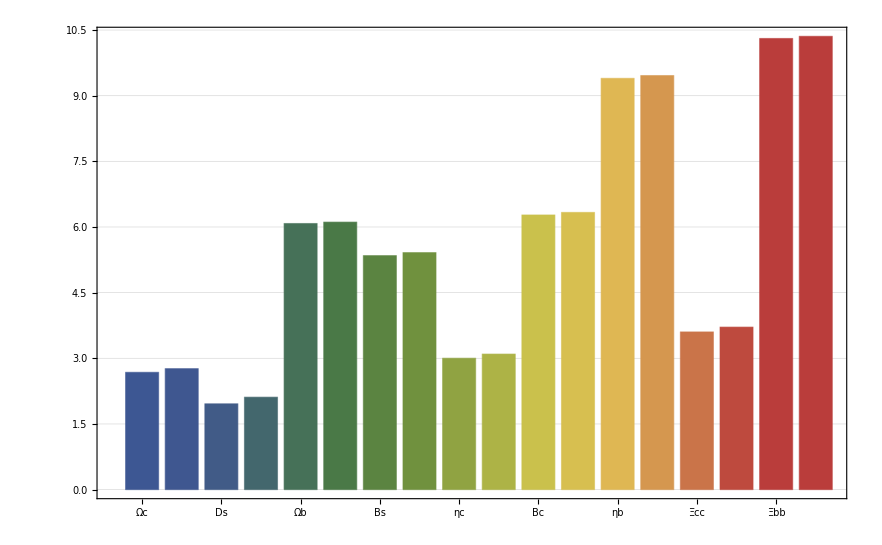

{My Error}

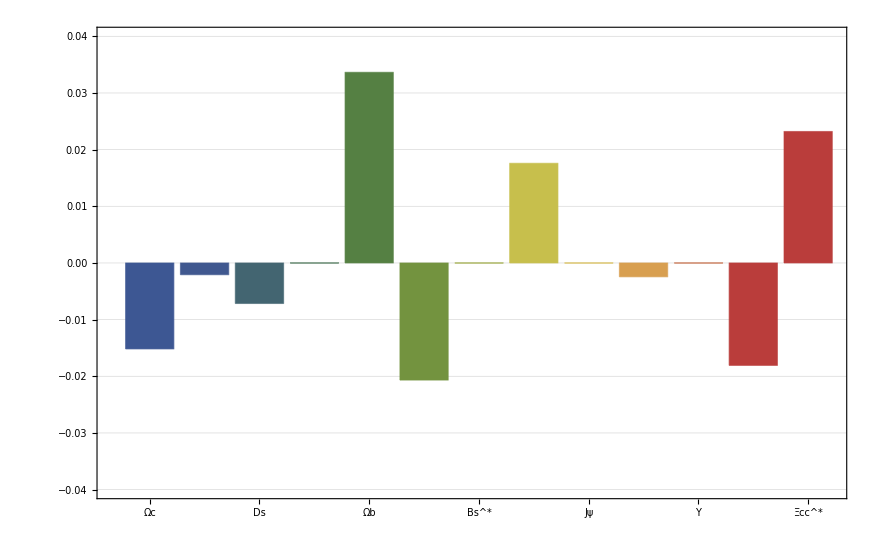

{Charge Radius}

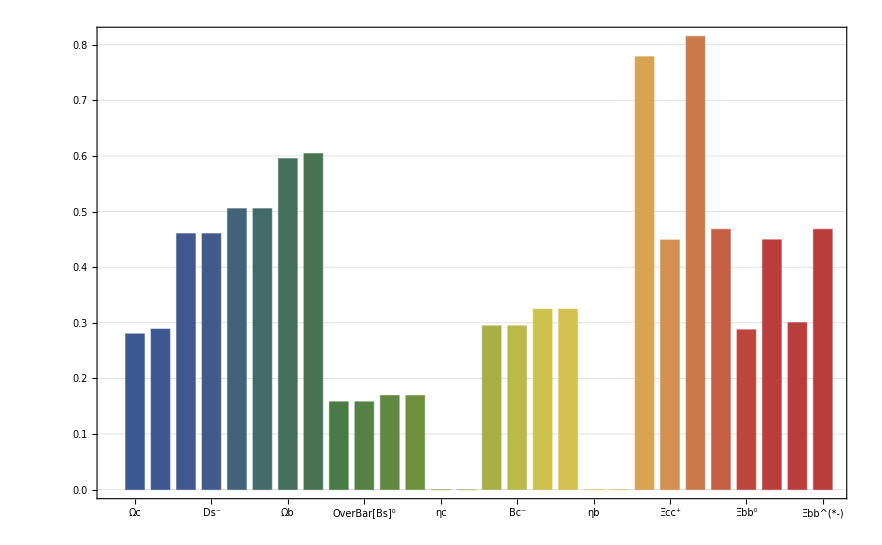

{Magnetic Moment}

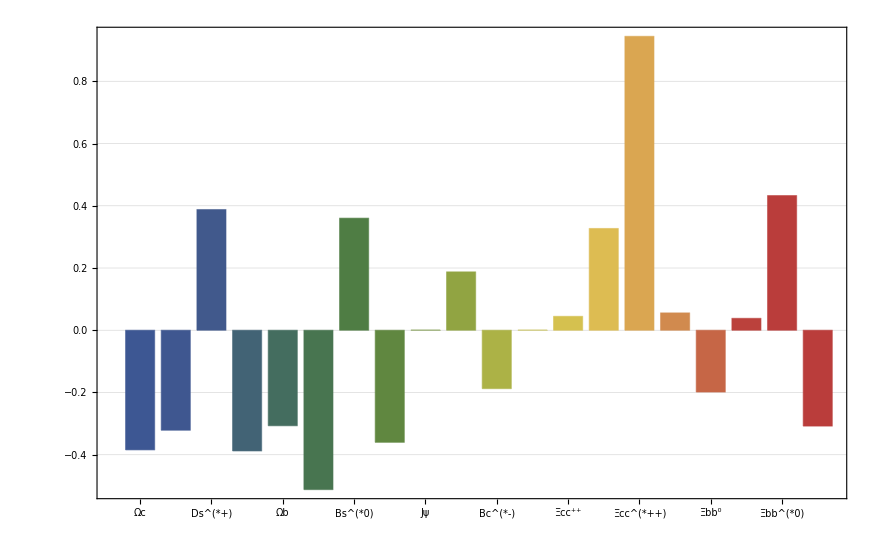

```mathematica
<<MITBagModel\MITBagModel.m

Nc=Hadron[{0,0,0,3},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,8}},0];
μNp=MagneticMoment[{0,0,0,4/3,-1/3},{0,0,0,0,0},Nc];

{"Binding Energy cs, bs, cc, bc, bb"}
Bcs=-(First[Hadron[{0,1,1,0},{{0,0,0,0},{0,0,-16/3,0},{0,0,0,0},{0,0,0,0}},0]]-2.112)/2
Bbs=-(First[Hadron[{1,0,1,0},{{0,0,-16/3,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},0]]-5.415)/2
Bcc=-(First[Hadron[{0,2,0,0},{{0,0,0,0},{0,-16/3,0,0},{0,0,0,0},{0,0,0,0}},0]]-3.097)/2
Bbc=-(First[Hadron[{1,1,0,0},{{0,16,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},0]]-6.275)/2
Bbb=-(First[Hadron[{2,0,0,0},{{-16/3,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},0]]-9.460)/2

{"Ωc 1/2+ 2.695"}
Ωc=Hadron[{0,1,2,0},{{0,0,0,0},{0,0,32/3,0},{0,0,-8/3,0},{0,0,0,0}},2Bcs]
rΩc=ChargeRadius[{0,1,2,0,0},{0,0,0,0,0},Ωc];
μΩc=MagneticMoment[{0,-1/3,4/3,0,0},{0,0,0,0,0},Ωc];
{rΩc}
{{μΩc},{μΩc/μNp}}

{"Ωc^* 3/2+ 2.766"}
SuperStar[Ωc]=Hadron[{0,1,2,0},{{0,0,0,0},{0,0,-16/3,0},{0,0,-8/3,0},{0,0,0,0}},2Bcs]
SuperStar[rΩc]=ChargeRadius[{0,1,2,0,0},{0,0,0,0,0},SuperStar[Ωc]];
SuperStar[μΩc]=MagneticMoment[{0,1,2,0,0},{0,0,0,0,0},SuperStar[Ωc]];
{SuperStar[rΩc]}
{{SuperStar[μΩc]},{SuperStar[μΩc]/μNp}}

{"Ds 0- 1.968"}
Ds=Hadron[{0,1,1,0},{{0,0,0,0},{0,0,16,0},{0,0,0,0},{0,0,0,0}},2Bcs]
rDsp=ChargeRadius[{0,1,0,0,0},{0,0,1,0,0},Ds];
rDsm=ChargeRadius[{0,0,1,0,0},{0,1,0,0,0},Ds];
{rDsp,rDsm}

{"Ds^* 1- 2.112"}
SuperStar[Ds]=Hadron[{0,1,1,0},{{0,0,0,0},{0,0,-16/3,0},{0,0,0,0},{0,0,0,0}},2Bcs]
SuperStar[rDsp]=ChargeRadius[{0,1,0,0,0},{0,0,1,0,0},SuperStar[Ds]];
SuperStar[rDsm]=ChargeRadius[{0,0,1,0,0},{0,1,0,0,0},SuperStar[Ds]];
SuperStar[μDsp]=MagneticMoment[{0,1,0,0,0},{0,0,1,0,0},SuperStar[Ds]];
SuperStar[μDsm]=MagneticMoment[{0,0,1,0,0},{0,1,0,0,0},SuperStar[Ds]];
{SuperStar[rDsp],SuperStar[rDsm]}
{{SuperStar[μDsp],SuperStar[μDsm]},{SuperStar[μDsp]/μNp,SuperStar[μDsm]/μNp}}

{"Ωb 1/2+ 6.046"}
Ωb=Hadron[{1,0,2,0},{{0,0,32/3,0},{0,0,0,0},{0,0,-8/3,0},{0,0,0,0}},2Bbs]
rΩb=ChargeRadius[{1,0,2,0,0},{0,0,0,0,0},Ωb];
μΩb=MagneticMoment[{-1/3,0,4/3,0,0},{0,0,0,0,0},Ωb];
{rΩb}
{{μΩb},{μΩb/μNp}}

{"Ωb^* 3/2+"}
SuperStar[Ωb]=Hadron[{1,0,2,0},{{0,0,-16/3,0},{0,0,0,0},{0,0,-8/3,0},{0,0,0,0}},2Bbs]
SuperStar[rΩb]=ChargeRadius[{1,0,2,0,0},{0,0,0,0,0},SuperStar[Ωb]];
SuperStar[μΩb]=MagneticMoment[{1,0,2,0,0},{0,0,0,0,0},SuperStar[Ωb]];
{SuperStar[rΩb]}
{{SuperStar[μΩb]},{SuperStar[μΩb]/μNp}}

{"Bs 0- 5.367"}
Bs=Hadron[{1,0,1,0},{{0,0,16,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},2Bbs]
rBs0=ChargeRadius[{0,0,1,0,0},{1,0,0,0,0},Bs];
rBs0bar=ChargeRadius[{1,0,0,0,0},{0,0,1,0,0},Bs];
{rBs0,rBs0bar}

{"Bs^* 1- 5.415"}
SuperStar[Bs]=Hadron[{1,0,1,0},{{0,0,-16/3,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},2Bbs]
SuperStar[rBs0]=ChargeRadius[{0,0,1,0,0},{1,0,0,0,0},SuperStar[Bs]];
SuperStar[rBs0bar]=ChargeRadius[{1,0,0,0,0},{0,0,1,0,0},SuperStar[Bs]];
SuperStar[μBs0]=MagneticMoment[{0,1,0,0,0},{0,0,1,0,0},SuperStar[Bs]];
SuperStar[μBs0bar]=MagneticMoment[{0,0,1,0,0},{0,1,0,0,0},SuperStar[Bs]];
{SuperStar[rBs0],SuperStar[rBs0bar]}
{{SuperStar[μBs0],SuperStar[μBs0bar]},{SuperStar[μBs0]/μNp,SuperStar[μBs0bar]/μNp}}

{"ηc 0- 2.984"}
ηc=Hadron[{0,2,0,0},{{0,0,0,0},{0,16,0,0},{0,0,0,0},{0,0,0,0}},2Bcc]
rηc=ChargeRadius[{0,1,0,0,0},{0,1,0,0,0},ηc];
{rηc}

{"Jψ 1- 3.097"}
Jψ=Hadron[{0,2,0,0},{{0,0,0,0},{0,-16/3,0,0},{0,0,0,0},{0,0,0,0}},2Bcc]
rJψ=ChargeRadius[{0,1,0,0,0},{0,1,0,0,0},Jψ];
μJψ=MagneticMoment[{0,1,0,0,0},{0,1,0,0,0},Jψ];
{rJψ}
{{μJψ},{μJψ/μNp}}

{"Bc 0- 6.275"}
Bc=Hadron[{1,1,0,0},{{0,16,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},2Bbc]
rBcp=ChargeRadius[{0,1,0,0,0},{1,0,0,0,0},Bc];
rBcm=ChargeRadius[{1,0,0,0,0},{0,1,0,0,0},Bc];
{rBcp,rBcm}

{"Bc^* 1-"}
SuperStar[Bc]=Hadron[{1,1,0,0},{{0,-16/3,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},2Bbc]
SuperStar[rBcp]=ChargeRadius[{0,1,0,0,0},{1,0,0,0,0},SuperStar[Bc]];
SuperStar[rBcm]=ChargeRadius[{1,0,0,0,0},{0,1,0,0,0},SuperStar[Bc]];
SuperStar[μBcp]=MagneticMoment[{0,1,0,0,0},{1,0,0,0,0},SuperStar[Bc]];
SuperStar[μBcm]=MagneticMoment[{1,0,0,0,0},{0,1,0,0,0},SuperStar[Bc]];
{SuperStar[rBcp],SuperStar[rBcm]}
{{SuperStar[μBcp],SuperStar[μBcm]},{SuperStar[μBcp]/μNp,SuperStar[μBcm]/μNp}}

{"ηb 0- 9.399"}
ηb=Hadron[{2,0,0,0},{{16,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},2Bbb]
rηb=ChargeRadius[{1,0,0,0,0},{1,0,0,0,0},ηb];
{rηb}

{"Υ 1- 9.460"}
Υ=Hadron[{2,0,0,0},{{-16/3,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},2Bbb]
rΥ=ChargeRadius[{1,0,0,0,0},{1,0,0,0,0},Υ];
μΥ=MagneticMoment[{1,0,0,0,0},{1,0,0,0,0},Υ];
{rΥ}
{{μΥ},{μΥ/μNp}}

{"Ξcc 1/2+ 3.621"}
Ξcc=Hadron[{0,2,0,1},{{0,0,0,0},{0,-8/3,0,32/3},{0,0,0,0},{0,0,0,0}},Bcc]
rΞccpp=ChargeRadius[{0,2,0,1,0},{0,0,0,0,0},Ξcc];
rΞccp=ChargeRadius[{0,2,0,0,1},{0,0,0,0,0},Ξcc];
μΞccpp=MagneticMoment[{0,4/3,0,-1/3,0},{0,0,0,0,0},Ξcc];
μΞccp=MagneticMoment[{0,4/3,0,0,-1/3},{0,0,0,0,0},Ξcc];
{rΞccpp,rΞccp}
{{μΞccpp,μΞccp},{μΞccpp/μNp,μΞccp/μNp}}

{"Ξcc^* 3/2+ 1.533"}
SuperStar[Ξcc]=Hadron[{0,2,0,1},{{0,0,0,0},{0,-8/3,0,-16/3},{0,0,0,0},{0,0,0,0}},Bcc]
SuperStar[rΞccpp]=ChargeRadius[{0,2,0,1,0},{0,0,0,0,0},SuperStar[Ξcc]];
SuperStar[rΞccp]=ChargeRadius[{0,2,0,0,1},{0,0,0,0,0},SuperStar[Ξcc]];
SuperStar[μΞccpp]=MagneticMoment[{0,2,0,1,0},{0,0,0,0,0},SuperStar[Ξcc]];
SuperStar[μΞccp]=MagneticMoment[{0,2,0,0,1},{0,0,0,0,0},SuperStar[Ξcc]];
{SuperStar[rΞccpp],SuperStar[rΞccp]}
{{SuperStar[μΞccpp],SuperStar[μΞccp]},{SuperStar[μΞccpp]/μNp,SuperStar[μΞccp]/μNp}}

{"Ξbb 1/2+"}
Ξbb=Hadron[{2,0,0,1},{{-8/3,0,0,32/3},{0,0,0,0},{0,0,0,0},{0,0,0,0}},Bbb]
rΞbb0=ChargeRadius[{2,0,0,1,0},{0,0,0,0,0},Ξbb];
rΞbbm=ChargeRadius[{2,0,0,0,1},{0,0,0,0,0},Ξbb];
μΞbb0=MagneticMoment[{4/3,0,0,-1/3,0},{0,0,0,0,0},Ξbb];
μΞbbm=MagneticMoment[{4/3,0,0,0,-1/3},{0,0,0,0,0},Ξbb];
{rΞbb0,rΞbbm}
{{μΞbb0,μΞbbm},{μΞbb0/μNp,μΞbbm/μNp}}

{"Ξbb^* 3/2+"}
SuperStar[Ξbb]=Hadron[{2,0,0,1},{{-8/3,0,0,-16/3},{0,0,0,0},{0,0,0,0},{0,0,0,0}},Bbb]
SuperStar[rΞbb0]=ChargeRadius[{2,0,0,1,0},{0,0,0,0,0},SuperStar[Ξbb]];
SuperStar[rΞbbm]=ChargeRadius[{2,0,0,0,1},{0,0,0,0,0},SuperStar[Ξbb]];
SuperStar[μΞbb0]=MagneticMoment[{2,0,0,1,0},{0,0,0,0,0},SuperStar[Ξbb]];
SuperStar[μΞbbm]=MagneticMoment[{2,0,0,0,1},{0,0,0,0,0},SuperStar[Ξbb]];
{SuperStar[rΞbb0],SuperStar[rΞbbm]}
{{SuperStar[μΞbb0],SuperStar[μΞbbm]},{SuperStar[μΞbb0]/μNp,SuperStar[μΞbbm]/μNp}}


{"Mass Spectrum"}
BarChart[{First[Ωc],First[SuperStar[Ωc]],First[Ds],First[SuperStar[Ds]],First[Ωb],First[SuperStar[Ωb]],First[Bs],First[SuperStar[Bs]],First[ηc],First[Jψ],First[Bc],First[SuperStar[Bc]],First[ηb],First[Υ],First[Ξcc],First[SuperStar[Ξcc]],First[Ξbb],First[SuperStar[Ξbb]]},Frame->True,ChartLabels->{"Ωc","Ωc^*","Ds","Ds^*","Ωb","Ωb^*","Bs","Bs^*","ηc","Jψ","Bc","Bc^*","ηb","Υ","Ξcc","Ξcc^*","Ξbb","Ξbb^*"},ChartStyle->"DarkRainbow",GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]

{"My Error"}
BarChart[{
(First[Ωc]-2.695),
(First[SuperStar[Ωc]]-2.766),
(First[Ds]-1.968),
(First[SuperStar[Ds]]-2.112),
(First[Ωb]-6.046),
(First[Bs]-5.367),
(First[SuperStar[Bs]]-5.415),
(First[ηc]-2.984),
(First[Jψ]-3.097),
(First[ηb]-9.399),
(First[Υ]-9.460),
(First[Ξcc]-3.621),
(First[SuperStar[Ξcc]]-3.690)},Frame->True,ChartLabels->{"Ωc","Ωc^*","Ds","Ds^*","Ωb","Bs","Bs^*","ηc","Jψ","ηb","Υ","Ξcc","Ξcc^*"},ChartStyle->"DarkRainbow",PlotRange->{-0.04,0.04},GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]

{"Charge Radius"}
BarChart[{rΩc,SuperStar[rΩc],rDsp,rDsm,SuperStar[rDsp],SuperStar[rDsm],rΩb,SuperStar[rΩb],rBs0,rBs0bar,SuperStar[rBs0],SuperStar[rBs0bar],rηc,rJψ,rBcp,rBcm,SuperStar[rBcp],SuperStar[rBcm],rηb,rΥ,rΞccpp,rΞccp,SuperStar[rΞccpp],SuperStar[rΞccp],rΞbb0,rΞbbm,SuperStar[rΞbb0],SuperStar[rΞbbm]},Frame->True,ChartLabels->{"Ωc","Ωc^*","Ds^+","Ds^-","Ds^(*+)","Ds^(*-)","Ωb","Ωb^*","Bs^0","OverBar[Bs]^0","Bs^(*0)","OverBar[Bs]^(*0)","ηc","Jψ","Bc^+","Bc^-","Bc^(*+)","Bc^(*-)","ηb","Υ","Ξcc^(++)","Ξcc^+","Ξcc^(*++)","Ξcc^(*+)","Ξbb^0","Ξbb^-","Ξbb^(*0)","Ξbb^(*-)"},ChartStyle->"DarkRainbow",GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]

{"Magnetic Moment"}
BarChart[{μΩc/μNp,SuperStar[μΩc]/μNp,SuperStar[μDsp]/μNp,SuperStar[μDsm]/μNp,μΩb/μNp,SuperStar[μΩb]/μNp,SuperStar[μBs0]/μNp,SuperStar[μBs0bar]/μNp,μJψ/μNp,SuperStar[μBcp]/μNp,SuperStar[μBcm]/μNp,μΥ/μNp,μΞccpp/μNp,μΞccp/μNp,SuperStar[μΞccpp]/μNp,SuperStar[μΞccp]/μNp,μΞbb0/μNp,μΞbbm/μNp,SuperStar[μΞbb0]/μNp,SuperStar[μΞbbm]/μNp},Frame->True,ChartLabels->{"Ωc","Ωc^*","Ds^(*+)","Ds^(*-)","Ωb","Ωb^*","Bs^(*0)","OverBar[Bs]^(*0)","Jψ","Bc^(*+)","Bc^(*-)","Υ","Ξcc^(++)","Ξcc^+","Ξcc^(*++)","Ξcc^(*+)","Ξbb^0","Ξbb^-","Ξbb^(*0)","Ξbb^(*-)"},ChartStyle->"DarkRainbow",GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]
```